```mathematica
ClearAll["Global`*"];
```

### Wprowadzenie wzoru na amplitudę drgań wymuszonych "A". "ao" - stosunek amplitudy siły wymuszającej do masy drgającego ciała, "ω_o" - częstotliwość kątowa drgań własnych układu, "Ω" - częstotliwość kątowa siły wymuszającej, "β" - współczynnik tłumienia.

```mathematica
A=ao/Sqrt[(ωo^2-Ω^2)^2+4×β^2×Ω^2];
```

### Obliczenie amplitudy drgań "A_o" w przypadku małej częstotliwości wymuszającej (przy granicy "Ω" zmierzającej do zera).

```mathematica
Ao=Limit[A,Ω->0]//PowerExpand;
```

### Wykorzystanie warunku istnienia ekstremum (pochodna równa zero) do obliczenia częstotliwości rezonansowej.

```mathematica
r1=Solve[D[A, Ω]==0,Ω]
```

{{Ω→0},{Ω→-√(-2 β^2+ωo^2)},{Ω→√(-2 β^2+ωo^2)}}

### Obliczenie częstotliwości rezonansowej "A_r".

```mathematica
Ar=A/.r1[[2,1]]//Simplify
```

ao/(2 √(-β^4+β^2 ωo^2))

### Obliczenie stosunku "stos" amplitudy rezonansowej do amplitudy w przypadku małej częstotliwości .

```mathematica
stos=Ar/Ao/.ωo^2->β^2+((2×π)/T)^2/.β->δ/T//Cancel//PowerExpand
```

(4 π^2+δ^2)/(4 π δ)

### Sporządzenie wykresu obrazującego zależność stosunku amplitudy rezonansowej do amplitudy w przypadku małej częstotliwości od logarytmicznego dekrementu tłumienia "δ".

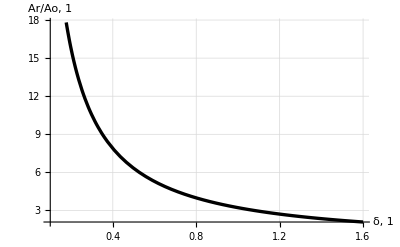

```mathematica
rys=Plot[stos,{δ,0.1,1.6},
BaseStyle->{FontFamily->"Times", FontSlant->"Italic", FontSize->12},
AxesLabel->{"δ, 1","Ar/Ao, 1"},
PlotStyle->{Black,Thickness[0.006]},GridLines->Automatic,GridLinesStyle->Directive[Gray]]
```